```mathematica
<<ACPackages`
```

### Построение системы и матриц

```mathematica
U[r_]:=1-r^2;
```

```mathematica
eqsϕr[λ_,k_,m_,Re_]:={-3 vr[r]+3 m^2 vr[r]+2 k^2 r^2 vr[r]+k^2 m^2 r^2 vr[r]+k^4 r^4 vr[r]-ⅈ k r^2 Re vr[r]+ⅈ k r^4 Re vr[r]-ⅈ k^3 r^4 Re vr[r]+ⅈ k^3 r^6 Re vr[r]+r^2 Re λ vr[r]+k^2 r^4 Re λ vr[r]-3 ⅈ m vϕ[r]+3 ⅈ m^3 vϕ[r]+3 ⅈ k^2 m r^2 vϕ[r]+k m r^2 Re vϕ[r]+k m r^4 Re vϕ[r]+ⅈ m r^2 Re λ vϕ[r]+3 r vr'[r]+m^2 r vr'[r]-2 k^2 r^3 vr'[r]+ⅈ k r^3 Re vr'[r]-ⅈ k r^5 Re vr'[r]-r^3 Re λ vr'[r]+3 ⅈ m r vϕ'[r]-ⅈ m^3 r vϕ'[r]-ⅈ k^2 m r^3 vϕ'[r]-k m r^3 Re vϕ'[r]+k m r^5 Re vϕ'[r]-ⅈ m r^3 Re λ vϕ'[r]-3 r^2 vr''[r]-m^2 r^2 vr''[r]-2 k^2 r^4 vr''[r]+ⅈ k r^4 Re vr''[r]-ⅈ k r^6 Re vr''[r]-r^4 Re λ vr''[r]-2 ⅈ m r^2 vϕ''[r]+2 r^3 Derivative[3][vr][r]+ⅈ m r^3 Derivative[3][vϕ][r]+r^4 Derivative[4][vr][r],ⅈ m vr[r]-ⅈ m^3 vr[r]-3 ⅈ k^2 m r^2 vr[r]-k m r^2 Re vr[r]-k m r^4 Re vr[r]-ⅈ m r^2 Re λ vr[r]-m^2 vϕ[r]+m^4 vϕ[r]+k^2 r^2 vϕ[r]+2 k^2 m^2 r^2 vϕ[r]+k^4 r^4 vϕ[r]-ⅈ k m^2 r^2 Re vϕ[r]-ⅈ k^3 r^4 Re vϕ[r]+ⅈ k m^2 r^4 Re vϕ[r]+ⅈ k^3 r^6 Re vϕ[r]+m^2 r^2 Re λ vϕ[r]+k^2 r^4 Re λ vϕ[r]-ⅈ m r vr'[r]-ⅈ m^3 r vr'[r]-ⅈ k^2 m r^3 vr'[r]-k m r^3 Re vr'[r]+k m r^5 Re vr'[r]-ⅈ m r^3 Re λ vr'[r]+m^2 r vϕ'[r]-k^2 r^3 vϕ'[r]+2 ⅈ m r^2 vr''[r]-m^2 r^2 vϕ''[r]-k^2 r^4 vϕ''[r]+ⅈ m r^3 Derivative[3][vr][r]};
```

```mathematica
(*КРС с целочисленной сеткой и одинаковыми разностями*)
```

```mathematica
FiniteMatrix4Eigen[n_,sample_:5,subst___]:=Block[{h=1/n,krseq,krs,unk,unkmain,unkfict,i,sm,s,order,lhs,rhs,gh,ω},
sm=Max[sample,5];
gh=(sm-1)/2;
unk=Join[Table[Subscript[f, i],{i,0-(sm-1)/2,n+(sm-1)/2}],Table[Subscript[g, i],{i,0-(sm-1)/2,n+(sm-1)/2}]];
unkmain=Join[Table[Subscript[f, i],{i,1,n-1}],Table[Subscript[g, i],{i,1,n-1}]];
unkfict=Complement[unk,unkmain];dersam[buk_,order_,s_]:=Table[Subscript[buk, j],{j,i-(s-1)/2,i+(s-1)/2}].NDCoefficientList[order,s]/h^order;
rhs=ω/k(f''[z]-k^2 f[z])/.{z->i h,f[z]->Subscript[f, i],f''[z]->dersam[2,sm],f''''[z]->dersam[4,sm]}/.{subst};
lhs=Simplify[(eqOZ[ω,k,R]+ω/k(f''[z]-k^2 f[z]))]/.{z->i h,f[z]->Subscript[f, i],f''[z]->dersam[2,sm],f''''[z]->dersam[4,sm]}/.{subst};
virfict={Subscript[f, -2]->6 Subscript[f, 0]-8 Subscript[f, 1]+3 Subscript[f, 2],Subscript[f, -1]->3 Subscript[f, 0]-3 Subscript[f, 1]+Subscript[f, 2],Subscript[f, 0]->0,Subscript[f, n]->0,Subscript[f, n+1]->3 Subscript[f, n]-3 Subscript[f, n-1]+Subscript[f, n-2],Subscript[f, n+2]->6 Subscript[f, n]-8 Subscript[f, n-1]+3 Subscript[f, n-2]};
fict=unkfict/.virfict;
rhs=Coefficient[#,unkmain]&/@(Table[rhs,{i,1,n-1}]/.virfict)/ω;
(*Print[rhs//TableForm];*)
lhs=Coefficient[#,unkmain]&/@(Table[lhs,{i,1,n-1}]/.virfict);
(*Print["next:"];
Print[lhs//TableForm];*)
(*Return[rhs.Inverse[lhs]];*)
Return[{lhs,rhs}];
];
```

```mathematica
(*КРС с дробной сеткой и центральными разностями-current*)
```

```mathematica
FiniteMatrix4Eigen[n_,m_,(*sample_:5,*)subst___]:=Block[{h=1/n,unk,unkmain,unkfict,i,sm,s,order,lhs,rhs,ω},
sm=Max[sample,5];
sm=5;
gh=(sm-1)/2;
unk=Join[Table[Subscript[f, i+1/2],{i,0-(sm-1)/2,n+(sm-1)/2-1}],Table[Subscript[g, i+1/2],{i,-1,n}]];
unkmain=Join[Table[Subscript[f, i],{i,1/2,n-1/2}],Table[Subscript[g, i],{i,1/2,n-1/2}]];
unkfict=Complement[unk,unkmain];
dersam[buk_,order_,s_]:=Table[Subscript[buk, j],{j,i-(s-1)/2,i+(s-1)/2}].NDCoefficientList[order,s]/h^order;
subs=Join[{r->i h},{vr[r_]->Subscript[f, i],vr'[r_]->dersam[f,1,sm],vr''[r_]->dersam[f,2,sm],vr'''[r_]->dersam[f,3,sm],vr''''[r_]->dersam[f,4,sm]},{vϕ[r_]->Subscript[g, i],vϕ'[r_]->dersam[g,1,sm],vϕ''[r_]->dersam[g,2,sm],vϕ'''[r_]->dersam[g,3,sm],vϕ''''[r_]->dersam[g,4,sm]},{subst}];
rhs=-D[eqsϕr[ω,k,m,R],ω]/.subs;
lhs=Simplify[(eqsϕr[ω,k,m,R]-ω D[eqsϕr[ω,k,m,R],ω])]/.subs;
bc={dersam[f,0,sm-1]/.i->n,(dersam[f,1,sm-1]+dersam[f,0,sm-1])/.i->n,dersam[g,0,sm-1]/.i->n};
bc=If[OddQ[m],Join[bc,{dersam[f,1,sm-1]/.i->0,dersam[g,1,sm-1]/.i->0,(dersam[f,0,sm-1]+ⅈ m dersam[g,0,sm-1])/.i->0}],Join[bc,{dersam[f,0,sm-1]/.i->0,dersam[g,0,sm-1]/.i->0,(dersam[f,1,sm-1]+ⅈ m dersam[g,1,sm-1])/.i->0}]];
virfict=First[Solve[Thread[bc==0],unkfict]];
fict=unkfict/.virfict;rhs=Coefficient[#,unkmain]&/@Flatten[Table[rhs,{i,1/2,n-1/2}]/.virfict];
lhs=Coefficient[#,unkmain]&/@Flatten[Table[lhs,{i,1/2,n-1/2}]/.virfict];
(*rhs=Coefficient[#,unk]&/@Join[Table[0,{i,2},{j,n+sm-1}],Table[rhs,{i,1/2,n-1/2}]/ω,Table[0,{i,2},{j,n+sm-1}]];
lhs=Coefficient[#,unk]&/@Join[{dersam[0,sm-1]/.i->0,dersam[1,sm-1]/.i->0},Table[lhs,{i,1/2,n-1/2}],{dersam[1,sm-1]/.i->n,dersam[0,sm-1]/.i->n}];*)
(*Return[rhs.Inverse[lhs]];*)
Return[{lhs,rhs}];
];
```

### Функции нахождения инкрементов

```mathematica
(*Получение с.з. и с.в. с помощью Eigen...[Inverse[a].m]*)
```

```mathematica
GetIncrements[n_,m_,k1_,R1_]:=Eigenvalues[Inverse[Last[#]].First[#]&[N[FiniteMatrix4Eigen[n,m,k->k1,R->R1]]]];
```

```mathematica
GetEigenWave[n1_,m_,k1_,R1_,mode_:1]:=Block[{eigval,eigvec,nom,syst},syst=Inverse[Last[#]].First[#]&[N[FiniteMatrix4Eigen[n1,m,k->k1,R->R1]]];
{eigval,eigvec}=Select[Transpose[Eigensystem[syst]],NumericQ[First[#]]&]//Transpose;
nom=Flatten[Position[eigval,Sort[eigval,Re[#1]>Re[#2]&]⟦mode⟧]]//First;
Print["Main eigen value is ",eigval[[nom]]];
Return[eigvec⟦nom⟧];];
```

```mathematica
(*Получение с.з. и с.в. с помощью Eigen...[{m,a}]*)
```

```mathematica
GetIncrements[n_,m_,k1_,R1_]:=Select[Eigenvalues[N[FiniteMatrix4Eigen[n,m,k->k1,R->R1]]],NumericQ];
```

```mathematica
GetEigenWave[n1_,m_,k1_,R1_,mode_:1]:=Block[{eigval,eigvec,nom,syst},syst=N[FiniteMatrix4Eigen[n1,m,k->k1,R->R1]];
{eigval,eigvec}=Select[Transpose[Eigensystem[syst]],NumericQ[First[#]]&]//Transpose;
nom=Flatten[Position[eigval,Sort[eigval,Re[#1]>Re[#2]&]⟦mode⟧]]//First;
Print["Main eigen value is ",eigval[[nom]]];
Return[eigvec⟦nom⟧];];
```

```mathematica
GetMainIncrement[n_,m_,k1_,R1_,num_:1]:=(*GetMainIncrement[n,k1,R1,num]=*)Take[Sort[Re/@GetIncrements[n,m,k1,R1]],{-num}]//First;
```

```mathematica
Take[Sort[GetIncrements[20,0,1,100],Re[#1]>Re[#2]&],10]
```

```mathematica
GetMainIncrement[20,0,1,100,2]
```

{20,1,100}

-0.274335

```mathematica
Sort[GetIncrements[20,0,10^-4,10],Re[#1]>Re[#2]&]
```

```mathematica
(*Отклонения в определителе после подстановки собственного значения
With[{n2=3,m=0,k2=1,R2=100,mod=1},Det[SetPrecision[First[#]-Sort[GetIncrements[n2,m,k2,R2],Re[#1]>Re[#2]&][[mod]]Last[#],1000]]&[SetPrecision[FiniteMatrix4Eigen[n2,m,k->k2,R->R2],1000]]]*)
```

```mathematica
(*Отклонения в векторе после подстановки собственных значений и векторов*)
With[{n2=300,m=0,k2=1,R2=1000,mod=2},(First[#]-Sort[GetIncrements[n2,m,k2,R2],Re[#1]>Re[#2]&][[mod]]Last[#]).GetEigenWave[n2,m,k2,R2,mod]&[FiniteMatrix4Eigen[n2,m,k->k2,R->R2]]]//Abs//PrintRange;
```

Main eigen value is -0.0904427+0.910558 ⅈ

```mathematica
?GetMainIncrement
```

GetMainIncrement[n_,m_,k1_,R1_,num_:1]:=First[Take[Sort[Re/@GetIncrements[n,m,k1,R1]],{-num}]]

```mathematica
ShowPlot[Re[Take[SortBy[N[GetIncrements[#,0,1,1]],Re],-5]]&,{5,200},All]
```

$Failed

```mathematica
ShowPlot[GetMainIncrement[Floor[#],0,1,1,2]&,{10,200},All,PlotPoints->5,MaxRecursion->1]
```

```mathematica
GetMainIncrement[100,#,1,1,2]&/@Range[0,5]
```

{-15.6747,-15.5291,-43.3152,-60.6134,-81.7302,-106.105}

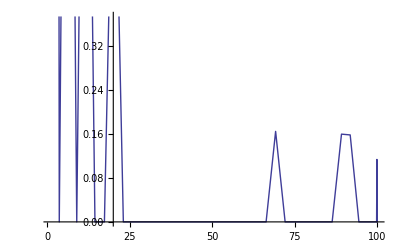

```mathematica
ShowPlot[-GetMainIncrement[100,0,0.001,#,2]&,{1,100}]
```

-0.235913

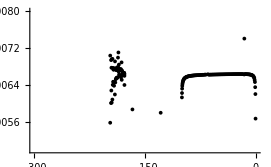

```mathematica
incrs=Sort[N[GetIncrements[100,2,0.01,300]],Re[#1]>Re[#2]&];
Print[Re[incrs⟦2⟧]];
Show[Graphics[{PointSize[0.01],(Point[{Re[#1],Im[#1]}]&)/@incrs}],Axes->True,PlotRange->{{-300,0},{0.005,0.008}},AspectRatio->1/GoldenRatio]
```

```mathematica
Sort[GetIncrements[300,1.,10000],Im[#1]<Im[#2]&]
```

### Визуализация собственных функций

Main eigen value is -15.5291+0.548844 ⅈ

{3.229,Null}

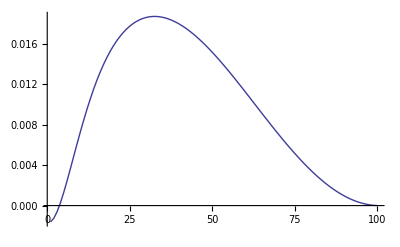
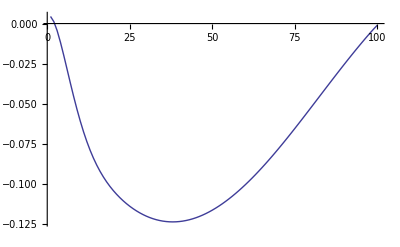

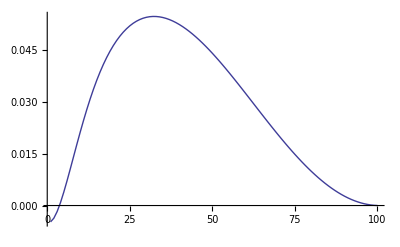
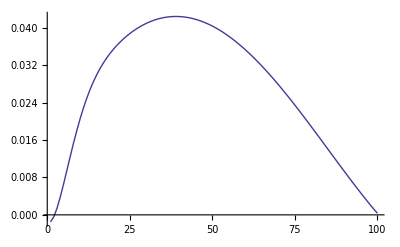

```mathematica
Timing[{ewvr,ewvϕ}=Partition[#,Length[#]/2]&[GetEigenWave[100,1,1,1,2]];]
PrintRange[Re[#]]&/@{ewvr,ewvϕ}
PrintRange[Im[#]]&/@{ewvr,ewvϕ}
```

```mathematica
With[{m=1},ListVectorPlot[Flatten[CutList[Table[{i/Length[ewvr]{Sin[u],Cos[u]},Re[E^(ⅈ m u)(ewvr⟦i⟧i/Length[ewvr]{Sin[u],Cos[u]}+ewvϕ⟦i⟧i/Length[ewvr]{-Cos[u],Sin[u]})]},{i,1,Length[ewvr]},{u,3π/2,5π/2,π/10}],50],1]]]
```

Main eigen value is -15.5291+0.548844 ⅈ

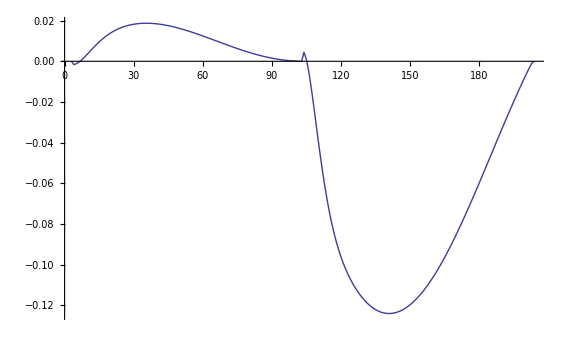

```mathematica
Block[{ew=Re/@GetEigenWave[100,1,1,1,2],fs},
fs=fict/.{Subscript[f, b_]:>ew[[b+1/2]]};
gr=PrintRange[alllist=Join[Take[fs,Length[fs]/2],ew,Take[fs,-Length[fs]/2]]]
]
```

### Различные зависимости инкрементов

#### От числа Рейнольдса Re

```mathematica
Plot[Re[GetMainIncrement[100,0,0.1,R,2]],{R,1,20000}]
```

```mathematica
{m=0,k=0.1,n=100}
```

```mathematica
{m=1,k=0.1,n=100}
```

```mathematica
{m=0,k=1,n=100}
```

```mathematica
{m=1,k=1,n=20}
```

```mathematica
linc=Table[{R,GetMainIncrement[100,0,1,R,2]},{R,1,20001,100}];
```

```mathematica
lincRe=Table[{R=10^logR,Take[Sort[GetIncrements[20,0,0.1,R],Re[#1]>Re[#2]&],10]},{logR,0,5,1/5}];
```

6.75 Second

Доказательство абсолютной устойчивости (есть сходимость по сетке и экспоненциальное приближение инкремента к нулю снизу

```mathematica
Plot[Log[10,-GetMainIncrement[150,1,0.01,Evaluate[10^logre],2]],{logre,0,7}]
```

```mathematica
Plot[Log[10,-GetMainIncrement[100,0,0.3,Evaluate[10^logre],2]],{logre,0,7}]
```

```mathematica
Plot[Log[10,-GetMainIncrement[50,0,0.001,Evaluate[10^logre],2]],{logre,0,7}]
```

```mathematica
Plot[Log[10,-GetMainIncrement[50,0,1,Evaluate[10^logre],2]],{logre,0,7}]
```

#### От размера сетки (сходимость) n

```mathematica
Timing[linc=Table[{n,(GetMainIncrement[n,0,1,1000,2])},{n,1,100,1}];]
```

```mathematica
Monitor[linc1=Table[{n,(Take[Sort[GetIncrements[n,0,1,1],Re[#1]>Re[#2]&],10])},{n,5,200,5}];,n]
```

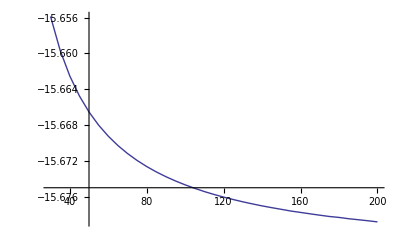

```mathematica
With[{nummod=2},gr=PrintRange[{#⟦1⟧,Re[#⟦2,nummod⟧]}&/@(Drop[linc1,5]/.{Take->(#1&)})]]
```

```mathematica
(*Нахождение пределов по размеру сетки*)
ListLimit[#,ApproximationReport->None]&/@(Transpose[{First/@Take[linc1,-Length[#]],#}]&/@Re[Transpose[Last/@Drop[linc1,8]]])
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{303093.,-15.683,-30.047,-50.218,-75.2488,-104.499,-142.082,-178.52,-227.035,-272.28}

#### От номера моды m

```mathematica
With[{n=50,k=0.05,R=10000},{GetMainIncrement[n,0,k,R,2],GetMainIncrement[n,1,k,R,2],GetMainIncrement[n,2,k,R,2],GetMainIncrement[n,3,k,R,2]}]
```

{50,0.05,10000}

{50,0.05,10000}

{-0.00632519,-0.00595565,-0.0116426,-0.0153648}

#### Списки инкрементов для нескольких мод и разных ситуаций

k=0.01; Re=1;m=2

{-26.4064,-71.1068,-136.016,-221.652,-328.649,-457.86,-610.198,-786.976,-989.322,-1219.1}

k=0.01; Re=1;m=1

{196811.,-14.6949,-49.3779,-104.211,-179.641,-276.275,-394.935,-536.609,-702.526,-894.069}

k=0.01; Re=1;m=0

{420085.,-14.6741,-30.4788,-49.221,-75.748,-103.473,-143.634,-177.501,-228.662,-270.915}

k=1; Re=1;m=0

{1.40202×10^6,-15.6829,-30.6978,-50.2175,-76.0955,-104.491,-143.759,-178.494,-229.029,-272.232}

k=0.1;Re=1;m=0

{1.40221×10^6,-14.692,-30.4131,-49.2277,-75.5854,-103.501,-143.388,-177.504,-228.506,-271.242}

k=1;Re=100;m=0

{14019.1,-0.273447,-0.320634,-0.459379,-0.783592,-1.0276,-1.43768,-1.77405,-2.28794,-2.71486}

#### От волнового числа вдоль канала k

```mathematica
Plot[GetMainIncrement[50,1,k,1000,2],{k,-0.1,2.3}]
```

```mathematica
Show[%71,%68]
```

```mathematica
If[!NumericQ[E],Remove[E]];
cutout=6;
ltest=Last/@Drop[linc,cutout];
{lnaλ,λ}=CoefficientList[Fit[Log[-dif[ltest]],{1,x},x],x];
a=-E^lnaλ/λ;Print[{a,λ}];
```

{-0.0057025-4.81507×10^-17 ⅈ,-0.00125945+9.67012×10^-18 ⅈ}

```mathematica
ListPlot[ltest-Table[a ⅇ^(λ x),{x,1,Length[ltest]}]]
```